## Appendix to manuscript entitled “Modifier Theory: The Population Genetics of Biological Noise” by DM Weinreich et al. Treats the toy model represented by Eqns 1 and 2 in that ms. Freely available under GNU General Public License (GPLv3)

#### 25 October 2025: Initial Version 28 October 2025: Tighten some comments; add Element[σ,PositiveReals]and Element[z0,Reals] to simplify interpretations of output.

If phenotype z_realized ~ N(z_0, σ^2) (Eqn 1 in ms) and Malthusian fitness r(z_realized) = r_optimum - z_realized^2 (Eqn 2 in ms), we seek the probability density function for z_realized using the change-of-value technique shown at https://online.stat.psu.edu/stat414/lesson/22/22.3. Elements of Figure 2 are also illustrated here.

As shown below, the pdf for z_realized is 

	fR[r,z_0,σ] = (ⅇ^(-(-√-r-z_0)^2/(2 σ^2)))/(2 √(2 π) σ √Abs[r])+(ⅇ^(-(√-r-z_0)^2/(2 σ^2)))/(2 √(2 π) σ √Abs[r])					Eqn A1

(Because selection acts on differences in Malthusian fitness, results are independent of r_optimum. So without loss of generality I set that to zero. The general solution would write r_optimum - r in place of r throughout Eqn A1.)

Using A1, we can now find the expected fitness effect of noise as a function of z_0 and σ, as well as it expectation conditioned on realizing a beneficial phenotype, i.e., on z_realized > z_0. Also as shown below, these are

	Er[z_0,σ] ≡ ∫_(-∞)^0 fR[[r,z_0,σ]rⅆr = -(z_0^2+σ^2)									Eqn A2

and

	ErBeneficial[z_0,σ]  ≡ (∫_(-z_0^2)^0 fR[r,z_0,σ]rⅆr)/(∫_(-z_0^2)^0 fR[r,z_0,σ]ⅆr) = 					Eqn A3
		{2 Abs[z_0] √(2/π) σ+(z_0^2+σ^2) 
(Erf[(z_0-√(z_0^2))/(√2 σ)]-Erf[(z_0+√(z_0^2))/(√2 σ)])}/Erf[(Abs[z_0] √2)/σ]		

Eqns A1 - A3  exactly match simulation results developed in MatLab (not shown).

Notation: fZ[] is the PDF of z_realized (Eq 1 in the ms), and v1[] and v2[] are the piece-wise inversions of the the function r(z_realized) = -r_realized^2 (Eq 2). fR[] is the PDF we seek.

```mathematica
fZ[z_,z0_,σ_] :=PDF[NormalDistribution[z0,σ],z];
v1[y_]:=-Sqrt[-y];
v2[y_]:=Sqrt[-y];
```

The recipe from the website is fR(r) = fZ(v1(r)) • |v1’(r)| + fZ(v2(r)) • |v2’(r)|

```mathematica
fR[r_,z0_,σ_]:=fZ[v1[r],z0,σ]*Abs[v1'[r]]+fZ[v2[r],z0,σ]*Abs[v2'[r]];
```

Say it out loud so that I can code it up in my MatLab simulations.

```mathematica
fR[r,z0,σ]
```

(ⅇ^(-(-√-r-z0)^2/(2 σ^2)))/(2 √(2 π) σ √Abs[r])+(ⅇ^(-(√-r-z0)^2/(2 σ^2)))/(2 √(2 π) σ √Abs[r])

Is it a PDF? Yes! (Though without the Element[σ,PositiveReals], Mathematica returns √(1/σ^2) σ.)

```mathematica
Clear[z0,σ];
$Assumptions=Element[σ,PositiveReals];
FullSimplify[∫_-Infinity^0 fR[r,z0,σ]ⅆr]
```

1

What is the expected fitness over all noise?

```mathematica
FullSimplify[∫_-Infinity^0 (fR[r,z0,σ]*r)ⅆr]
```

-z0^2-σ^2

```mathematica
Er[z0_,σ_]:=-(z0^2+σ^2);
```

Finally, the expected fitness over beneficial noise? First the numerator.

```mathematica
Refine[FullSimplify[∫_(-(z0^2))^0 (fR[r,z0,σ]*r)ⅆr],Element[z0,Reals]]
```

1/2 (2 √(2/π) σ Abs[z0]+(z0^2+σ^2) (Erf[(z0-Abs[z0])/(√2 σ)]-Erf[(z0+Abs[z0])/(√2 σ)]))

And now the denominator, needed to make our result a PDF.

```mathematica
Refine[FullSimplify[∫_(-(z0^2))^0 fR[r,z0,σ]ⅆr],Element[z0,Reals]]
```

Piecewise[{{-1/2 Erf[(√2 z0)/σ], z0<0}, {1/2 Erf[(√2 z0)/σ], z0>0}, {0, True}}]

Looking at the above suggests that the denominator is 1/2 Abs[Erf[(z0 √2)/σ]], giving

```mathematica
ErBeneficial[z0_,σ_]:=( Abs[z0] √(2/π) σ+1/2(z0^2+σ^2) (Erf[(z0-√(z0^2))/(√2 σ)]-Erf[(z0+√(z0^2))/(√2 σ)]))/(1/2 Abs[Erf[(z0 √2)/σ]]);
```

#### Figures

Here’s the y-axis of Figure 2A. The second panel illustrates that the peak at r_optimum in the first is extremely narrow, so I truncated it from the ms to reduce confusion for the reader.

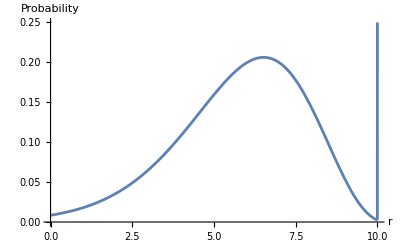

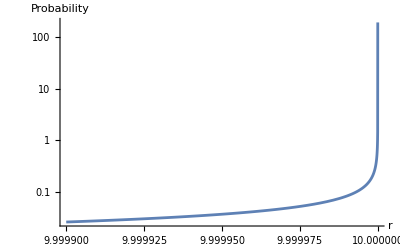

```mathematica
ropt=10;
z0=-2;
σLowNoise=0.5;
Plot[fR[r-ropt,z0,σLowNoise],{r,0,10},PlotRange->{0,0.25},AxesLabel->{"r","Probability"}]
LogPlot[fR[r-ropt,z0,σLowNoise],{r,9.9999,10},PlotRange->All,AxesLabel->{"r","Probability"}]
```

Here’s the y-axis for Figure 2B

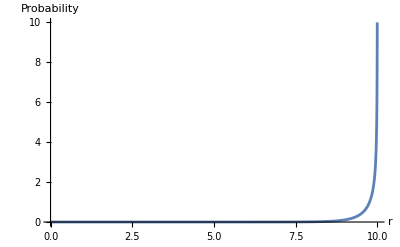

```mathematica
z0=0;
Plot[fR[r-ropt,z0,σLowNoise],{r,0,10},AxesLabel->{"r","Probability"},PlotRange->{0,10}]
```

Here’s Figure 2C (the vanishingly narrow spike at r = 10 for the low-noise plot in blue was again omitted from the figure).

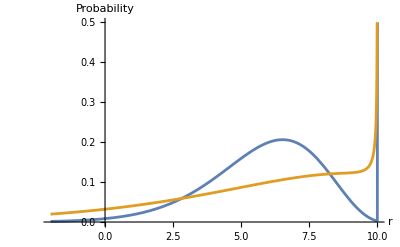

```mathematica
z0=-2;
σHighNoise=1;
Plot[{fR[r-ropt,z0,σLowNoise],fR[r-ropt,z0,σHighNoise]},{r,-2,10},PlotRange->{0,.5},AxesLabel->{"r","Probability"}]
```

Here’s Fig 2D

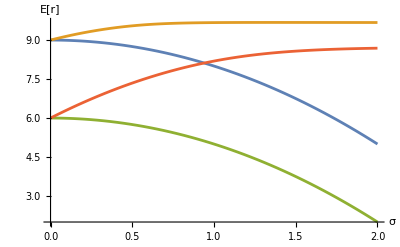

```mathematica
Plot[{ropt+Er[1,σ],ropt+ErBeneficial[1,σ],ropt+Er[2,σ],ropt+ErBeneficial[2,σ]},{σ,0,2},AxesLabel->{"σ","E[r]"}]
```